```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
qpData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,qpData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
momentumAvail= Normal[DeleteDuplicates[ds[Take,"momentum"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"momentum"->momentumAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_,invX_ :True]:=(
data=Apply[ds,directive];
x=(data[Take,keys[[1]]]//Normal);
y=(data[Take,keys[[2]]]//Normal);
If[invX,x=1/x];
result=Table[{x[[it]],y[[it]]},{it,Length[x]}];
Clear[x,y];
result
)
```

```mathematica
charCast[value_,type_]:=Alphabet[][[Position[qpAvail[type],value][[1,1]]]];
```

```mathematica
makeFits[data_,func_,arg_,points_]:=Table[Fit[d[[-Min[points,Length[d]];;-1]],func,arg],{d, data}];
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,IntegerPart[x],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

```mathematica
getPlot[data_,func_, arg_,points_]:=(
SetOptions[LinTicks,TickLengthScale->2.5];
SetOptions[MaTeX,Magnification->1.9];

label=If[k==0.0,"(a)",If[k==0.5,"(a)",If[k==1.0,"(c)",""]]];

colors=Table[If[B<=1.0,Blend[{Purple,Orange},1-Sqrt[1-B]],Blend[{Red,Blue},1-Sqrt[B-1]]],{B,qpAvail["interaction"]//Normal}];
pltStyle=Table[Directive[color,Opacity[0.7]],{color,colors}];
fpltStyle=Table[Directive[Dashed,color,Opacity[0.7]],{color,colors}];

fs=22;
plt=ListPlot[data,
PlotRange->{{0,0.1},{0,0.6}},ImageSize->360,Joined->False,
Frame->True,Axes->False,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
PlotMarkers->{"●", 14},
(*
PlotLegends->If[k==0.5,Placed[
PointLegend[Table[
MaTeX[StringJoin["\\lambda = ",ToString[NumberForm[B,{2,1}]]],Magnification->1.55],
{B,qpAvail["interaction"]//Normal}],Spacings->0.0,LegendLayout->"Row"],
{0.5,0.85}],None],
*)
Epilog->{
Inset[
MaTeX["\\text{"<>label<>" }"],
Scaled[{-0.187,1.05}]]
(*Inset[
MaTeX["(t\\text{--}J)",Magnification->2],
Scaled[{0.5,0.75}],Scaled[{0,0}]]*)
(*Inset[PointLegend[
Table[If[B<=1.0,Blend[{Purple,Orange},1-Sqrt[1-B]],Blend[{Red,Blue},1-Sqrt[B-1]]],{B,{0.0,1.0}}],
Table[MaTeX[StringJoin["\\lambda = ",ToString[NumberForm[B,{2,1}]]],Magnification->1.55],{B,{0.0,1.0}}],
Spacings->{0,0.5},LegendLayout->"Row",LegendMarkerSize->16],Scaled[{0.01,0.82}],Scaled[{0,0}]]
,
Inset[PointLegend[
Table[If[B<=1.0,Blend[{Purple,Orange},1-Sqrt[1-B]],Blend[{Red,Blue},1-Sqrt[B-1]]],{B,{0.5,0.9,1.1}}],
Table[MaTeX[StringJoin["\\lambda = ",ToString[NumberForm[B,{2,1}]]],Magnification->1.55],{B,{0.5,0.9,1.1}}],
Spacings->{0,0.5},LegendLayout->"Row",LegendMarkerSize->16],Scaled[{0.01,0.68}],Scaled[{0,0}]]*)
},
FrameLabel->{MaTeX["L^{-1}"],MaTeX["\\Delta E~/~t"]},
LabelStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
PlotStyle->pltStyle,
AspectRatio->.75,
FrameTicks->{{LinTicks[0,0.8,0.2,8,TickLabelFunction->tlf],StripTickLabels[LinTicks[0,0.8,0.2,8]]},{LinTicks[0,0.1,0.05,10,TickLabelFunction->tlf],StripTickLabels[LinTicks[0,0.1,0.05,10]]}}
];

fits=makeFits[data,func,arg,points];
fplt=Plot[fits,{x,0,1/10},PlotStyle->fpltStyle];

Show[plt,fplt,PlotRangeClipping->False]
)
```

```mathematica
makePlotsGapL[]:=(
fitFunctions=If[k==0.5,{1,x,x/Log[1/x]},{1,x}];
fitPoints=5;

directive={Select[#coupling==J&&#momentum==k&&#interaction==B&]};
keys={"size","gap"};

plots={};
Do[(
Do[(
gap={};
Do[(
AppendTo[gap,extractData[qpDataset,directive,keys]];
),{B,qpAvail["interaction"]//Normal}];
AppendTo[plots,{getPlot[Pick[gap,EvenQ[1/gap[[;;,;;,1]]/1]],fitFunctions, x,fitPoints]}];
),{k,qpAvail["momentum"]//Normal}];
),{J,qpAvail["coupling"]//Normal}];

plots
)
```

J ∈ {0.4} @ 12-2-24_1.0-0.1-1.0

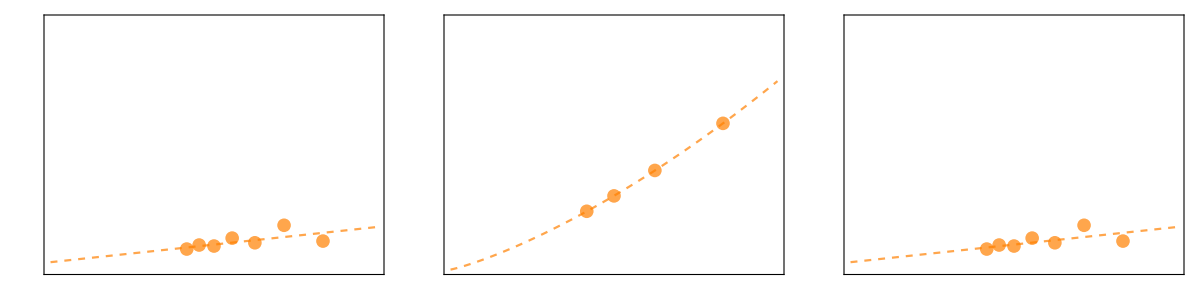

```mathematica
JRange={"0.4"};
tails={"12-2-24_1.0-0.1-1.0"};
(*tails={"12-2-28_0.5-0.4-0.9","12-2-28_1.1-0.1-1.1"};*)
gapPlots={};
Do[(
qpDataset=Dataset[getAssoc["qp",JRange,tail]];
qpAvail=Dataset[getStruct[qpDataset]];
Print[Style[StringJoin["J ∈ ",ToString[JRange]," @ ", tail],16]];
AppendTo[gapPlots,makePlotsGapL[]];
kDim=Length[qpAvail["momentum"]];
plots=ArrayReshape[gapPlots[[-1]],{Length[gapPlots[[-1]]]/kDim,kDim}];
Print[Grid[plots]];
),{tail,tails}]
```

```mathematica
SavePlots[]:=(
Do[(
Do[(
fileName=StringJoin["plots/scaling/gap/",
"gap_J=",ToString[qpAvail["coupling"][[iJ]]],
"_k=",ToString[qpAvail["momentum"][[ik]]],
".jpg"];
Export[fileName,gapPlots[[1,(iJ-1)*Length[qpAvail["momentum"]//Normal]+ik,1]],ImageResolution->300];
),{ik,Length[qpAvail["momentum"]//Normal]}]
),{iJ,Length[qpAvail["coupling"]//Normal]}]
)
```

```mathematica
(*SavePlots[]*)
```

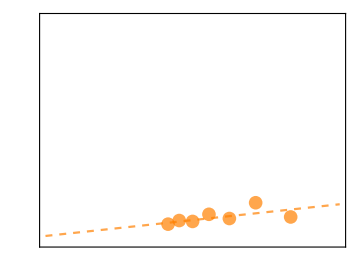
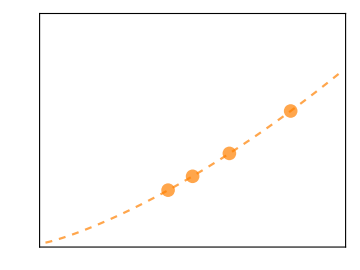
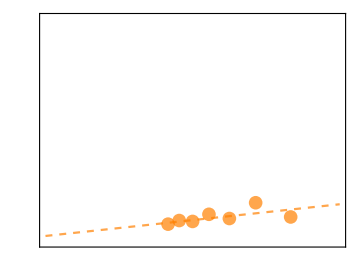

```mathematica
gapPts=Table[Show[gapPlots[[;;,l,1]]],{l,3}]
```

```mathematica
Export["/Users/pwrzosek/Desktop/XY/DeltaE_pi_2.png",gapPts[[3]],ImageResolution->300];
```

```mathematica
leg01=PointLegend[
Table[If[B<=1.0,Blend[{Purple,Orange},1-Sqrt[1-B]],Blend[{Red,Blue},1-Sqrt[B-1]]],{B,{0.0,1.0}}],
Table[MaTeX[StringJoin["\\lambda = ",ToString[NumberForm[B,{2,1}]]],Magnification->2],{B,{0.0,1.0}}],
Spacings->{0,1.0},LegendLayout->"Column",LegendMarkerSize->20]
```

```mathematica
leg02=PointLegend[
Table[If[B<=1.0,Blend[{Purple,Orange},1-Sqrt[1-B]],Blend[{Red,Blue},1-Sqrt[B-1]]],{B,{0.5,0.9,1.1}}],
Table[MaTeX[StringJoin["\\lambda = ",ToString[NumberForm[B,{2,1}]]],Magnification->2],{B,{0.5,0.9,1.1}}],
Spacings->{0,1.0},LegendLayout->"Column",LegendMarkerSize->20]
```

```mathematica
(*Export["/Users/pwrzosek/Desktop/spin_polaron_figs/fig5c.png",leg02,ImageResolution->300];*)
```

```mathematica
gapPlots[[1,2,1]]
```

-Graphics-

```mathematica
Export["t-XY_E.png",gapPlots[[1,2,1]],ImageResolution->300];
```